## Definitions and Setup

```mathematica
hbarc = 0.197326938; (* GeV fm *)
```

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica

## Plot setup

```mathematica
SetOptions[Plot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[LogPlot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListPlot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListLogPlot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

## Primordial cross sections and branching (feed down) matrix

```mathematica
splitHyperfine[x_] := {x[[1]],x[[2]],x[[3]],x[[3]],x[[3]],x[[4]],x[[5]],x[[5]],x[[5]]}
```

#### From PDG for Upsilon states

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
(*decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,0.7355,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,0.9806,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,0.648,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,0.82,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,0.8283,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,0.9824,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,0.6946,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,0.8289}(* χb2(2P) *)
} ;*)
```

```mathematica
decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,1,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,1,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,1,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,1,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,1,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,1,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,1,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,1}(* χb2(2P) *)
} ;
```

```mathematica
1-Total[{0.1153,0.181,0,0.0091}]
```

0.6946

```mathematica
Total /@ decayMatrix
```

{1,1.2645,1.0194,1.352,1.18,1.1717,1.0176,1.3054,1.1711}

```mathematica
feeddownMatrix = Transpose[decayMatrix];
MatrixForm[feeddownMatrix]
```

(1 | 0.2645 | 0.0194 | 0.352 | 0.18 | 0.0657 | 0.0038 | 0.1153 | 0.077
0 | 1 | 0 | 0 | 0 | 0.106 | 0.0138 | 0.181 | 0.089
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0091 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0051
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### LHC 5 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *) 
sigmasEXP = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}
```

{57.6,19,3.72,13.69,16.1,6.8,3.27,12.,14.15}

```mathematica
sigmas = Inverse[feeddownMatrix].sigmasEXP
```

{43.0147,14.8027,3.72,13.5808,16.0278,6.8,3.27,12.,14.15}

#### Compute 1S branching fractions and check sum rule

```mathematica
plucker1s = Table[If[i==j && i==1,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];plucker2s = Table[If[i==j && i==2,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker1p = Table[If[i==j && i≥3 && i ≤5,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker3s = Table[If[i==j && i==6,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker2p = Table[If[i==j && i≥7 && i ≤9,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
```

```mathematica
(feeddownMatrix.plucker1s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.746783

```mathematica
(feeddownMatrix.plucker2s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0679743

```mathematica
(feeddownMatrix.plucker1p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.134334

```mathematica
(feeddownMatrix.plucker3s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.00775625

```mathematica
(feeddownMatrix.plucker2p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0431524

```mathematica
0.7467833958680554+0.0679743142013889+0.13433367881944444``+0.007756249999999999+0.043152361111111114
```

## Data files

```mathematica
dataDir = "output_1kNpTraj";
```

```mathematica
labelMap = Association[
{"./"-> "κ̂ = 6, γ̂ = 0"}
];
```

```mathematica
datafile = "/input/"<>dataDir<>"/datafile.gz";
```

## Read in data

```mathematica
rawDataAll=Partition[Import[wd<>datafile,"Table"],2];
Length[rawDataAll]
```

2000

```mathematica
selectL[lval_]:=Select[rawDataAll,#[[2,8]]==lval&]
```

```mathematica
rawDataS = selectL[0];
Length[rawDataS]
rawDataP = selectL[1];
Length[rawDataP]
```

1000

1000

```mathematica
myR = RandomInteger[{1,Length[rawDataS]}]
rawDataS[[myR ]]
rawDataP[[myR ]]
```

231

{{4.71035,0.211335,-0.0847076,0.0372197,1.7606,2.34991,0.0372197},{0.734314,0.456022,0,0.308775,0,0,0,0}}

{{4.71035,0.211335,-0.0847076,0.0372197,1.7606,2.34991,0.0372197},{0,0,0.899846,0,0.41732,0,0,1}}

```mathematica
sData=Transpose[{rawDataS[[All,2,1]], rawDataS[[All,2,2]], rawDataP[[All,2,3]], rawDataS[[All,2,4]], rawDataP[[All,2,5]], rawDataS[[All,2,6]]}];
mData = rawDataS[[All,1]];
rawData = Partition[Riffle[mData,sData],2];
```

```mathematica
bVals=rawData[[All,1,1]]//Union
```

{4.71035}

```mathematica
Length[bVals]
```

1

## Glauber stuff for 5 TeV Pb-Pb collisions

```mathematica
(* This was computed externally for a 5.023 TeV PB-PB collision with sigmaNN = 62 *)
nPartVals={406.12232235261763,374.9882778251423,315.8591222901291,243.53796282970384,168.50283662224285,112.39007027735359,70.7871426138262,41.05093670919672,21.292761520545895,9.667790836200798,3.8095328022884103,0.970598659138994};
```

```mathematica
Transpose[{bVals,nPartVals}]
```

Transpose::nmtx: The first two levels of {1⟦All,Riffle[Riffle[Partition[],{Partition[],Partition[],Partition[],Partition[],Partition[],Partition[]}]]⟧,{406.122,374.988,315.859,«6»,9.66779,3.80953,0.970599}} cannot be transposed.

Transpose[{1⟦All,Riffle[Riffle[Partition[],{Partition[],Partition[],Partition[],Partition[],Partition[],Partition[]}]]⟧,{406.122,374.988,315.859,243.538,168.503,112.39,70.7871,41.0509,21.2928,9.66779,3.80953,0.970599}}]

```mathematica
nPartVsBInt = Interpolation[Transpose[{bVals,nPartVals}]];
```

Transpose::nmtx: The first two levels of {1⟦All,Riffle[Riffle[Partition[],{Partition[],Partition[],Partition[],Partition[],Partition[],Partition[]}]]⟧,{406.122,374.988,315.859,«6»,9.66779,3.80953,0.970599}} cannot be transposed.

Interpolation::innd: First argument in {1⟦All,Riffle[Riffle[Partition[],{Partition[],Partition[],Partition[],Partition[],Partition[],Partition[]}]]⟧,{«1»}}^T does not contain a list of data and coordinates.

```mathematica
Plot[nPartVsBInt[b],{b,bVals[[1]],bVals[[-1]]},PlotStyle->Black,FrameLabel->{"b","N_part"}]
```

Plot::plln: Limiting value Riffle[Riffle[Partition[],{Partition[],Partition[],Partition[],Partition[],Partition[],Partition[]}]] in {b,1,Riffle[Riffle[Partition[],{Partition[],Partition[],Partition[],Partition[],Partition[],Partition[]}]]} is not a machine-sized real number.

Plot[nPartVsBInt[b],{b,bVals⟦1⟧,bVals⟦-1⟧},PlotStyle→Black,FrameLabel→{b,N_part}]

```mathematica
bvscData = Import[wd<>"/input/glauber-data/bvscData.tsv"];
```

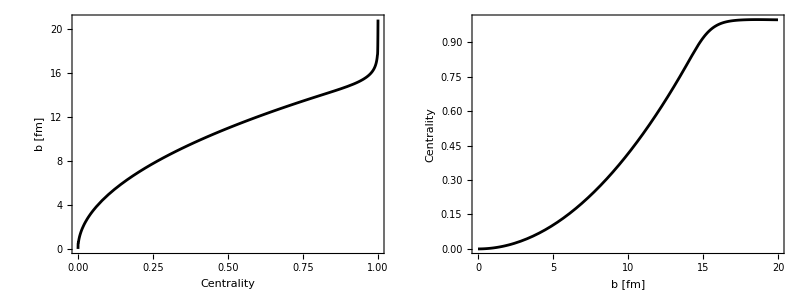

```mathematica
bVsCInt = Interpolation[bvscData];
cVsBInt = Interpolation[Map[Reverse,bvscData]];
Grid[{{Plot[bVsCInt[c],{c,0,1},PlotStyle->Black,FrameLabel->{"Centrality","b [fm]"}],
Plot[cVsBInt[b],{b,0,20},PlotStyle->Black,FrameLabel->{"b [fm]","Centrality"}]}}]
```

```mathematica
cVals=cVsBInt[bVals];
pFunction[c_] = Exp[-c/0.25]/Integrate[Exp[-x/0.25],{x,0,1}]
(*pFunction[c_] = Exp[-c/0.2]/Integrate[Exp[-x/0.2],{x,0,1}]*)
```

4.07463 ⅇ^(-4. c)

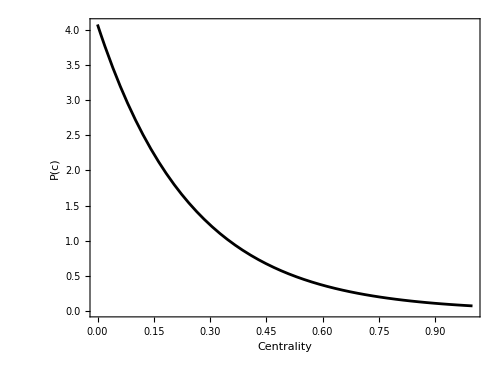

```mathematica
Plot[pFunction[c],{c,0,1},PlotStyle->Black,FrameLabel->{"Centrality","P(c)"}]
```

```mathematica
nbinvsbData = Import[wd<>"/input/glauber-data/nbinvsbData.tsv"];
```

```mathematica
nbinVsb = Interpolation[nbinvsbData]; (* units are fm^2 *)
```

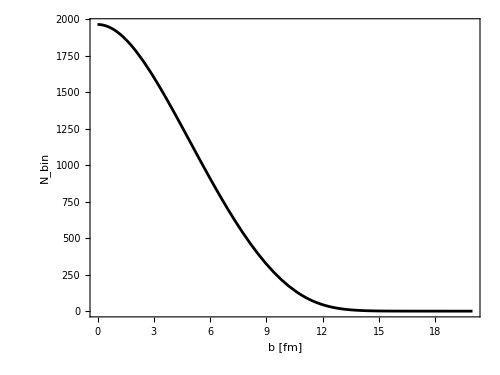

```mathematica
Plot[nbinVsb[b],{b,0,20},PlotStyle->Black,FrameLabel->{"b [fm]","N_bin"}]
```

## Primordial cross sections and branching (feed down) matrix

```mathematica
splitHyperfine[x_] := {x[[1]],x[[2]],x[[3]],x[[3]],x[[3]],x[[4]],x[[5]],x[[5]],x[[5]]}
```

#### From PDG for Upsilon states

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,1,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,1,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,1,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,1,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,1,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,1,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,1,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,1}(* χb2(2P) *)
} ;
```

```mathematica
1-Total[{0.1153,0.181,0,0.0091}]
```

0.6946

```mathematica
Total /@ decayMatrix
```

{1,1.2645,1.0194,1.352,1.18,1.1717,1.0176,1.3054,1.1711}

```mathematica
feeddownMatrix = Transpose[decayMatrix];
MatrixForm[feeddownMatrix]
```

(1 | 0.2645 | 0.0194 | 0.352 | 0.18 | 0.0657 | 0.0038 | 0.1153 | 0.077
0 | 1 | 0 | 0 | 0 | 0.106 | 0.0138 | 0.181 | 0.089
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0091 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0051
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### LHC 5 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *) sigmasEXP = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}
```

{57.6,19,3.72,13.69,16.1,6.8,3.27,12.,14.15}

```mathematica
sigmas = Inverse[feeddownMatrix].sigmasEXP
```

{43.0147,14.8027,3.72,13.5808,16.0278,6.8,3.27,12.,14.15}

#### Compute 1S branching fractions and check sum rule

```mathematica
plucker1s = Table[If[i==j && i==1,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];plucker2s = Table[If[i==j && i==2,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker1p = Table[If[i==j && i≥3 && i ≤5,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker3s = Table[If[i==j && i==6,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker2p = Table[If[i==j && i≥7 && i ≤9,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
```

```mathematica
fFracs={(feeddownMatrix.plucker1s.sigmas)[[1]]/sigmasEXP[[1]],
(feeddownMatrix.plucker2s.sigmas)[[1]]/sigmasEXP[[1]],
(feeddownMatrix.plucker1p.sigmas)[[1]]/sigmasEXP[[1]],
(feeddownMatrix.plucker3s.sigmas)[[1]]/sigmasEXP[[1]],
(feeddownMatrix.plucker2p.sigmas)[[1]]/sigmasEXP[[1]]}
Total[fFracs]
```

{0.746783,0.0679743,0.134334,0.00775625,0.0431524}

1.

## Results as a function of impact parameter/centrality (no feed down)

```mathematica
selectB[i_]:=Select[rawData,#[[1,1]]==bVals[[i]]&] 
rAAvsB[i_]:=selectB[i][[All,2]][[All,1;;6]] 
rAAavgVsB[i_]:=Mean[rAAvsB[i]]
rAAsdevVsB[i_] :=StandardDeviation[rAAvsB[i]]/Sqrt[Length[rAAvsB[i]]]
```

```mathematica
results=ParallelTable[Join[{bVals[[i]]},Riffle[rAAavgVsB[i],rAAsdevVsB[i]]],{i,1,Length[bVals]}]
```

Partition::argb: Partition called with 0 arguments; between 2 and 6 arguments are expected.

```mathematica
pointMapNP[x_]:= {nPartVsBInt[x[[1]]],Around[x[[2]],x[[3]]]};
raa1sNP = Sort[pointMapNP/@results[[All,{1,2,3}]],#1[[1]]<#2[[1]]&];
raa2sNP = Sort[pointMapNP/@results[[All,{1,4,5}]],#1[[1]]<#2[[1]]&] ;
raa2pNP = Sort[pointMapNP/@results[[All,{1,6,7}]],#1[[1]]<#2[[1]]&] ;
raa3sNP = Sort[pointMapNP/@results[[All,{1,8,9}]],#1[[1]]<#2[[1]]&] ;
raa3pNP = Sort[pointMapNP/@results[[All,{1,10,11}]],#1[[1]]<#2[[1]]&] ;
```

```mathematica
npartPlot=ListPlot[{raa1sNP,raa2sNP,raa2pNP,raa3sNP,raa3pNP},PlotRange->{{0,nPartVals[[1]]*1.01},Automatic},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->{Automatic,Medium},IntervalMarkers->"Bands",FrameLabel->{"N_part","R_AA"},PlotLegends->Placed[LineLegend[{Style["1S",16],Style["2S",16],Style["1P",16],Style["3S",16],Style["2P",16]},LegendMarkerSize->{{60,12}}],{0.85,0.7}],PlotLabel->Style[labelMap[dataDir],18]]
```

-Graphics-

## Results as a function of impact parameter/centrality (with feed down)

```mathematica
nAAavgVsB[i_]:=0.1 sigmas splitHyperfine[ rAAavgVsB[i]] nbinVsb[bVals[[i]]]
nAAsdevVsB[i_]:=0.1sigmas splitHyperfine[ rAAsdevVsB[i]] nbinVsb[bVals[[i]]]
```

```mathematica
results=Table[Join[{bVals[[i]]},Riffle[nAAavgVsB[i],nAAsdevVsB[i]] ],{i,1,Length[bVals]}]
```

{{4.70318,4553.99,29.9703,1424.23,21.1182,522.256,3.06954,1906.63,11.2061,2250.17,13.2253,595.754,12.7399,353.822,5.28485,1298.43,19.3939,1531.06,22.8687}}

```mathematica
pointMap[x_]:= {x[[1]],Around[10^(-6)x[[2]],10^(-6)x[[3]]]};
naa1s = pointMap/@results[[All,{1,2,3}]] ;
naa2s = pointMap/@results[[All,{1,4,5}]] ;
naa2p0 = pointMap/@results[[All,{1,6,7}]] ;
naa2p1 = pointMap/@results[[All,{1,8,9}]] ;
naa2p2= pointMap/@results[[All,{1,10,11}]] ;
naa3s = pointMap/@results[[All,{1,12,13}]] ;
naa3p0 = pointMap/@results[[All,{1,14,15}]] ;
naa3p1= pointMap/@results[[All,{1,16,17}]] ;
naa3p2 = pointMap/@results[[All,{1,18,19}]] ;
```

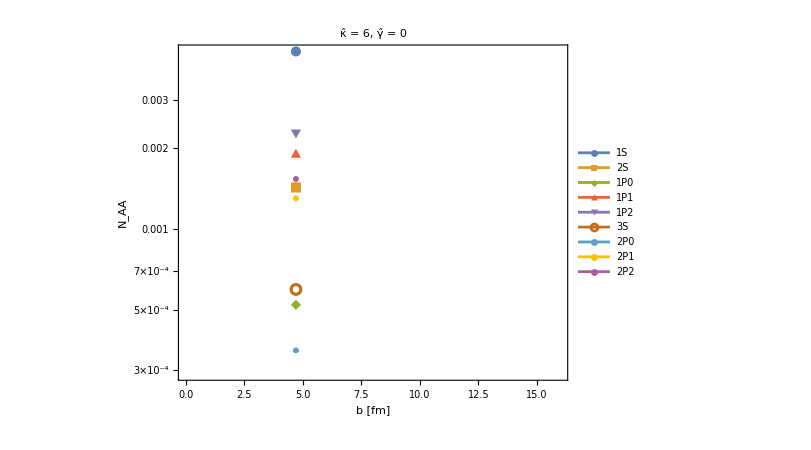

```mathematica
ListLogPlot[{naa1s,naa2s,naa2p0,naa2p1,naa2p2,naa3s,naa3p0,naa3p1,naa3p2},PlotRange->{{0,16},Automatic},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->{Automatic,Medium},IntervalMarkers->"Bands",FrameLabel->{"b [fm]","N_AA"},PlotLegends->Placed[LineLegend[{Style["1S",16],Style["2S",16],Style["1P0",16],Style["1P1",16],Style["1P2",16],Style["3S",16],Style["2P0",16],Style["2P1",16],Style["2P2",16]},LegendMarkerSize->{{60,12}}],Right],PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
computeRAAwithFeeddown := Module[{i,j,d,avg,err},
ParallelTable[
d=feeddownMatrix.Table[nbinVsb[bVals[[i]]]*sigmas[[j]]*0.1,{j,1,9}] ; (* denominator of RAA *)
avg= feeddownMatrix.nAAavgVsB[i];
err= feeddownMatrix.nAAsdevVsB[i];
Table[Around[avg[[j]],err[[j]]],{j,1,9}]/d
,{i,1,Length[bVals]}]
]
```

```mathematica
myRes=computeRAAwithFeeddown
```

{{0.9030.007,0.8070.012,1.1550.007,1.1530.007,1.1530.007,0.7210.015,0.8900.013,0.8900.013,0.8900.013}}

```mathematica
raa1sNP = Sort[Transpose[{nPartVsBInt[bVals],myRes[[All,1]]}],#1[[1]]<#2[[1]]&];
raa2sNP = Sort[Transpose[{nPartVsBInt[bVals],myRes[[All,2]]}],#1[[1]]<#2[[1]]&];
raa3sNP = Sort[Transpose[{nPartVsBInt[bVals],myRes[[All,6]]}],#1[[1]]<#2[[1]]&];
```

Transpose::nmtx: The first two levels of {Interpolation[{{4.70318},{406.122,«10»,0.970599}}^T][{4.70318}],{0.903}} cannot be transposed.

Transpose::nmtx: The first two levels of {Interpolation[{{4.70318},{406.122,«10»,0.970599}}^T][{4.70318}],{0.807}} cannot be transposed.

Transpose::nmtx: The first two levels of {Interpolation[{{4.70318},{406.122,«10»,0.970599}}^T][{4.70318}],{0.721}} cannot be transposed.

```mathematica
withFDnp=ListPlot[{raa1sNP,raa2sNP,raa3sNP},PlotRange->{{0,408},Automatic},Joined->True,InterpolationOrder->1,IntervalMarkers->"Bands",FrameLabel->{"N_part","R_AA"},
PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMargins->20,LegendMarkerSize->{{49,15}}],{Right,Top}],PlotLabel->Style[labelMap[dataDir],18]]
```

-Graphics-